```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=Flatten[Import["./k1.dat"]];
kappa=Flatten[Import["./y13.dat"]];
Zphi=Flatten[Import["./y10.dat"]];
etaphi=Flatten[Import["./etaphi.dat"]];
etapsi=Flatten[Import["./etapsi.dat"]];
(*fpi=Flatten[Import["./fpi.dat"]];
T=Flatten[Import["./TMeV.dat"]];
ListPlot[Transpose[{T,fpi}](*,ScalingFunctions->{"Log",Automatic}*),PlotRange->All]*)
```

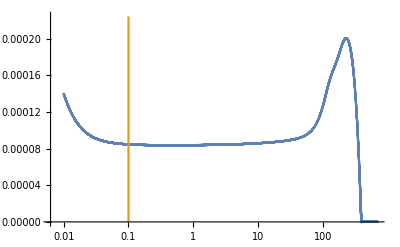

```mathematica
ListLinePlot[{Transpose[{k,kappa/k}],{{0.1,0},{0.1,1}}},ScalingFunctions->{"Log",Automatic}]
```

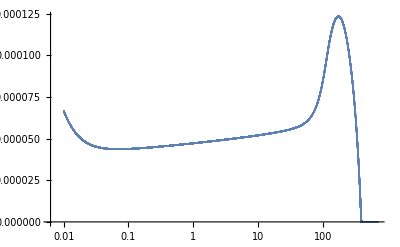

```mathematica
ListPlot[Transpose[{k,kappa/(Zphi k)}],ScalingFunctions->{"Log",Automatic}]
```

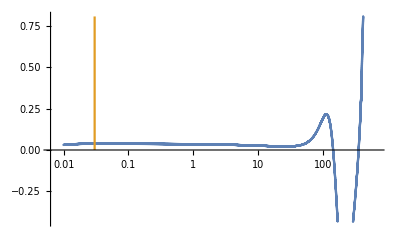

```mathematica
ListLinePlot[{Transpose[{k,etaphi}],{{0.03,0},{0.03,1}}},ScalingFunctions->{"Log",Automatic}]
```